## Techniques Final

### 2

#### b

```mathematica
Quantity[, "PlanckConstant"]*Quantity[, "SpeedOfLight"]/Quantity[1.12, "Electronvolts"]//UnitConvert
```

1.107×10^-6 m

#### d

Total shifts: 2048 parallel shifts down, and 2048^2 serial shifts out.  
Total cycles: #shifts*3
Total time: #cycles/rate

```mathematica
(2048+2048^2)shifts*3 cycles/shifts/(10^7 cycles/Quantity[, "Seconds"])//N
```

1.25891 s

#### e

CTE is % of electrons successfully moved during one pixel shift
How many times is the last pixel moved?  It’s moved 2048 times parallel and 2048 times serially.
And fraction=CTE^(2048+2048)

```mathematica
(.999)^(2*2048)
```

0.016605

```mathematica
ScientificForm[0.016605034169726227]
```

1.6605×10^-2

### 4

```mathematica
SNR[n_, npix_,b_,d_,ρ_,t_]:=n *t/√(n*t+2npix(b*t+d*t+ρ))
```

#### a

```mathematica
SNR[45 /Quantity[, "Seconds"],9p ,1.4/Quantity[, "Seconds"] /p, 2 /Quantity[, "Seconds"]/p,4 /p,t Quantity[, "Seconds"]]//FullSimplify
```

(45 t)/(√(72.+106.2 t))

Read noise dominates

#### b

```mathematica
SNR[45 /Quantity[, "Seconds"],25p ,1.4/Quantity[, "Seconds"] /p, 4 /Quantity[, "Seconds"]/p,4 /p,25 Quantity[, "Seconds"]]//FullSimplify
```

12.5193

moon brightness dominates

### 6

```mathematica
data={{1.2,8.56},{1.5,8.57}}
```

{{1.2,8.56},{1.5,8.57}}

```mathematica
m=LinearModelFit[data,X,X]
```

FittedModel[8.52+0.0333333 X]

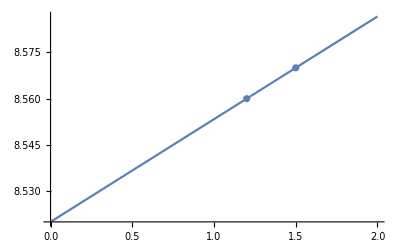

```mathematica
Show[Plot[m[X],{X,0,2}],ListPlot[data]]
```

#### a

```mathematica
k=m["BestFitParameters"][[2]]
```

0.0333333

```mathematica
mi=m[0]
```

8.52